## Extrapolation of Quantum Vertex Amplitude

```mathematica
ResourceFunction["DraculaTheme"][]
```

```mathematica
QVamp= Import["/home/ri47hud/codes/Frusta quantum amplitude/Cluster Files/Q_amps/SU2_Vamp_full.csv"];
SemiVamp = Import["/home/ri47hud/codes/Frusta quantum amplitude/Cluster Files/Q_amps/SU2_Vamp_semi_large.csv"];
```

```mathematica
spinmax = 100;
```

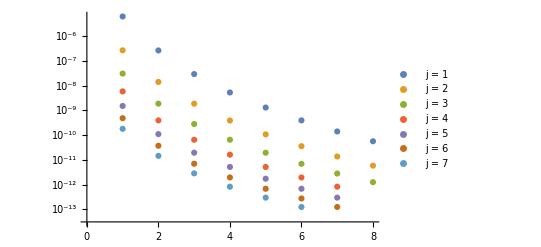

```mathematica
ListLogPlot[{QVamp[[1]],QVamp[[2]],QVamp[[3]],QVamp[[4]],QVamp[[5]], QVamp[[6]], QVamp[[7]]}, PlotLegends->{"j = 1","j = 2","j = 3","j = 4", "j = 5","j = 6","j = 7"}]
```

Plot the relative error (s-q)/q and (s-q)/s for different j with k varying.

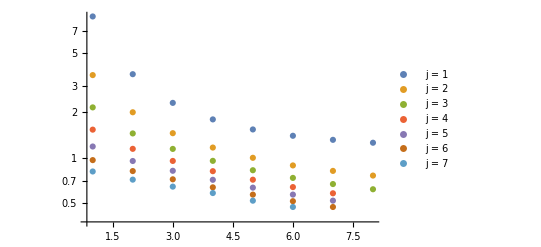

```mathematica
ListLogPlot[Join[Array[Abs[SemiVamp[[#,1;;8]]-QVamp[[#,1;;8]]]/QVamp[[#,1;;8]] &,3,1],Array[Abs[SemiVamp[[#,1;;7]]-QVamp[[#,1;;7]]]/QVamp[[#,1;;7]] &,3,4],Array[Abs[SemiVamp[[#,1;;6]]-QVamp[[#,1;;6]]]/QVamp[[#,1;;6]] &,1,7]], PlotLegends->{"j = 1","j = 2", "j = 3","j = 4","j = 5","j = 6","j = 7"},PlotRange->All]
```

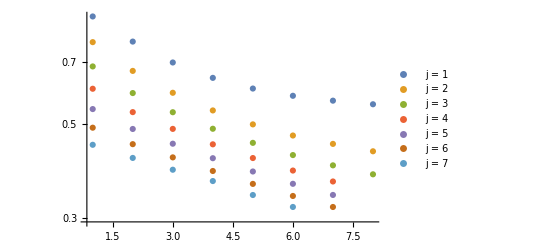

```mathematica
ListLogPlot[Join[Array[Abs[SemiVamp[[#,1;;8]]-QVamp[[#,1;;8]]]/SemiVamp[[#,1;;8]] &,3,1],Array[Abs[SemiVamp[[#,1;;7]]-QVamp[[#,1;;7]]]/SemiVamp[[#,1;;7]] &,3,4],Array[Abs[SemiVamp[[#,1;;6]]-QVamp[[#,1;;6]]]/SemiVamp[[#,1;;6]] &,1,7]], PlotLegends->{"j = 1","j = 2", "j = 3","j = 4","j = 5","j = 6","j = 7"},PlotRange->All]
```

{a→-0.135719,b→-0.0274831,c→1.22375}

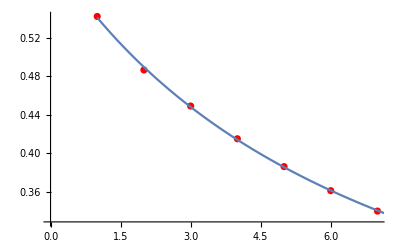

```mathematica
j = 5;
fitti = FindFit[Abs[SemiVamp[[j,1;;7]]-QVamp[[j,1;;7]]]/SemiVamp[[j,1;;7]],a/(Exp[b*x]-c),{{a,-0.5},{b,-0.1},c},x]
Show[ListPlot[Abs[SemiVamp⟦j,1;;7⟧-QVamp⟦j,1;;7⟧]/SemiVamp⟦j,1;;7⟧,PlotStyle->Red],Plot[a/(Exp[b x]-c)/.fitti,{x,1,8}]]
```

After testing, it seems that the (s-q)/s error seems to be better suited for fitting than (s-q)/q. One might also argue from the perspective that q carries a numerical error while s follows an analytical formula.

Plot the same data but transposed to see which is better suited for fitting.

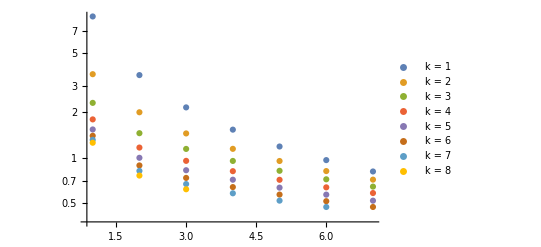

```mathematica
ListLogPlot[Join[Array[Abs[SemiVamp[[1;;7,#]]-QVamp[[1;;7,#]]]/QVamp[[1;;7,#]] &,6],Array[Abs[SemiVamp[[1;;6,#]]-QVamp[[1;;6,#]]]/QVamp[[1;;6,#]] &,1,7],Array[Abs[SemiVamp[[1;;3,#]]-QVamp[[1;;3,#]]]/QVamp[[1;;3,#]] &,1,8]], PlotLegends->{"k = 1","k = 2", "k = 3","k = 4","k = 5","k = 6","k = 7","k = 8"},PlotRange->All]
```

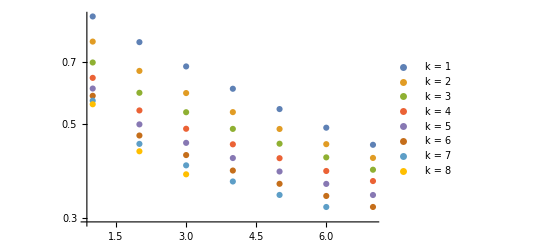

```mathematica
ListLogPlot[Join[Array[Abs[SemiVamp[[1;;7,#]]-QVamp[[1;;7,#]]]/SemiVamp[[1;;7,#]] &,6],Array[Abs[SemiVamp[[1;;6,#]]-QVamp[[1;;6,#]]]/SemiVamp[[1;;6,#]] &,1,7],Array[Abs[SemiVamp[[1;;3,#]]-QVamp[[1;;3,#]]]/SemiVamp[[1;;3,#]] &,1,8]], PlotLegends->{"k = 1","k = 2", "k = 3","k = 4","k = 5","k = 6","k = 7","k = 8"},PlotRange->All]
```

We considered several functions for fitting and apparently, the exponential decay with non-zero limit works well

```mathematica
jmodel[x_,a_,b_,c_]:=a/(Exp[b*x]-c);
ks=Symbol["k"<>ToString[#]]& /@Range[7];
as=Symbol["a"<>ToString[#]]& /@Range[7];
bs=Symbol["b"<>ToString[#]]& /@Range[7];
cs=Symbol["c"<>ToString[#]]& /@Range[7];
fits1 = Array[Function[i,FindFit[((SemiVamp[[i,1;;8]]-QVamp[[i,1;;8]])/SemiVamp[[i,1;;8]]),jmodel[ks[[i]],as[[i]],bs[[i]],cs[[i]]],{{as[[i]],-0.8},{bs[[i]],-0.2},{cs[[i]],1.0}},ks[[i]]]],3,1];
fits2 = Array[Function[i,FindFit[((SemiVamp[[i,1;;7]]-QVamp[[i,1;;7]])/SemiVamp[[i,1;;7]]),jmodel[ks[[i]],as[[i]],bs[[i]],cs[[i]]],{{as[[i]],-0.8},{bs[[i]],-0.2},{cs[[i]],1.0}},ks[[i]]]],3,4];
fits3 = Array[Function[i,FindFit[((SemiVamp[[i,1;;6]]-QVamp[[i,1;;6]])/SemiVamp[[i,1;;6]]),jmodel[ks[[i]],as[[i]],bs[[i]],cs[[i]]],{{as[[i]],-0.8},{bs[[i]],-0.2},{cs[[i]],1.0}},ks[[i]]]],1,7];
fits = Join[fits1,fits2,fits3];
relerrVampK = Table[jmodel[k,as[[j]],bs[[j]],cs[[j]]]/.fits[[j]],{j,7},{k,spinmax}];
ExtraVampK = Table[SemiVamp[[j,k]]*(1-relerrVampK[[j,k]]),{j,7},{k,spinmax}];
kmodel[x_,a_,b_,c_]:=a/(Exp[b*x]-c);
js=Symbol["j"<>ToString[#]]& /@Range[spinmax];
ds=Symbol["d"<>ToString[#]]& /@Range[spinmax];
es=Symbol["e"<>ToString[#]]& /@Range[spinmax];
fs=Symbol["f"<>ToString[#]]& /@Range[spinmax];
jfits = Array[FindFit[(SemiVamp[[1;;7,#]]-ExtraVampK[[1;;7,#]])/SemiVamp[[1;;7,#]],kmodel[js[[#]],ds[[#]],es[[#]],fs[[#]]],{{ds[[#]],-0.3},{es[[#]],-0.1},{fs[[#]],1.5}},js[[#]]]&,spinmax,1];
relerrVamp = Table[kmodel[j,ds[[k]],es[[k]],fs[[k]]]/.jfits[[k]],{j,spinmax},{k,spinmax}];
ExtraVamp = Table[SemiVamp[[j,k]]*(1-relerrVamp[[j,k]]),{j,spinmax},{k,spinmax}];
Export["/home/ri47hud/codes/Frusta quantum amplitude/Cluster Files/SU2_Vamp_extra.csv", ExtraVamp, "CSV"];
```

General::munfl: Exp[-708.434] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-708.664] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-708.893] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of FindFit::sszero will be suppressed during this calculation.

General::munfl: 1/(4.49556×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/(4.497×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/(4.49841×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

$Aborted

Part::partd: Part specification relerrVamp⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification relerrVamp⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification relerrVamp⟦1,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

## Extrapolation of Quantum Edge Amplitude

```mathematica
QEamp= Import["/ssd/ri47hud/codes/Frusta quantum amplitude/Cluster Files/SU2_Eamp_full.csv"];
SemiEamp = Import["/ssd/ri47hud/codes/Frusta quantum amplitude/Cluster Files/SU2_Eamp_semi.csv"];
```

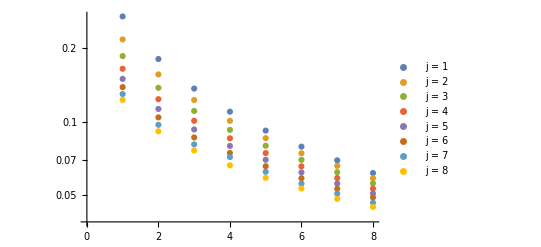

```mathematica
ListLogPlot[Array[Abs[SemiEamp[[#,1;;8]]-QEamp[[#,1;;8]]]/QEamp[[#,1;;8]] &,8], PlotLegends->{"j = 1","j = 2", "j = 3","j = 4","j = 5","j = 6","j = 7","j = 8"}]
```

```mathematica
-Graphics-Abs[SemiVamp[[#,1;;8]]-QVamp[[#,1;;8]]]/SemiVamp[[#,1;;8]]
```

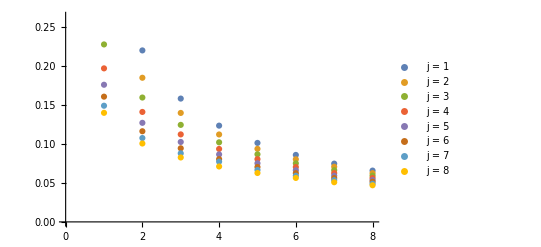

```mathematica
ListPlot[Array[Abs[SemiEamp[[#,1;;8]]-QEamp[[#,1;;8]]]/SemiEamp[[#,1;;8]] &,8], PlotLegends->{"j = 1","j = 2", "j = 3","j = 4","j = 5","j = 6","j = 7","j = 8"}]
```

```mathematica
-Graphics-Abs[SemiVamp[[#,1;;8]]-QVamp[[#,1;;8]]]/SemiVamp[[#,1;;8]]
```

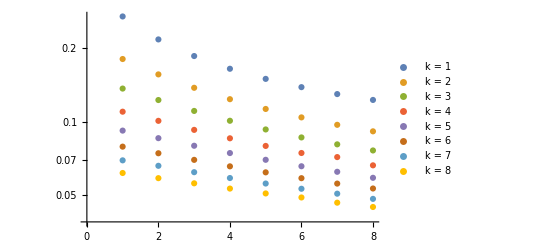

```mathematica
ListLogPlot[Array[Abs[SemiEamp[[1;;8,#]]-QEamp[[1;;8,#]]]/QEamp[[1;;8,#]] &,8], PlotLegends->{"k = 1","k = 2", "k = 3","k = 4","k = 5","k = 6","k = 7","k = 8"}]
```

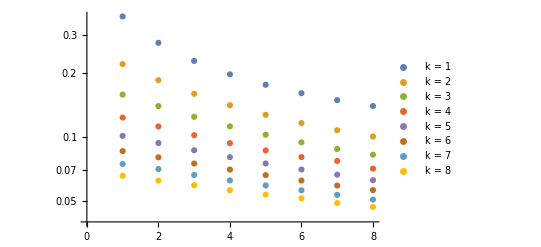

```mathematica
ListLogPlot[Array[Abs[SemiEamp[[1;;8,#]]-QEamp[[1;;8,#]]]/SemiEamp[[1;;8,#]] &,8], PlotLegends->{"k = 1","k = 2", "k = 3","k = 4","k = 5","k = 6","k = 7","k = 8"}]
```

```mathematica
spinmax = 1000;
jmodel[x_,a_,b_,c_]:=a*Exp[-b*x]+c;
js=Symbol["j"<>ToString[#]]& /@Range[spinmax];
as=Symbol["a"<>ToString[#]]& /@Range[spinmax];
bs=Symbol["b"<>ToString[#]]& /@Range[spinmax];
cs=Symbol["c"<>ToString[#]]& /@Range[spinmax];
fits = Array[Function[i,FindFit[(Abs[SemiEamp[[1;;8,i]]-QEamp[[1;;8,i]]]/SemiEamp[[1;;8,i]]),jmodel[js[[i]],as[[i]],bs[[i]],cs[[i]]],{as[[i]],bs[[i]],cs[[i]]},js[[i]]]],8];
RelerrEampJ = Table[jmodel[j,as[[k]],bs[[k]],cs[[k]]]/.fits[[k]],{j,spinmax},{k,8}];
ExtraEampJ = Table[SemiEamp[[j,k]]*(1+RelerrEampJ[[j,k]]),{j,spinmax},{k,8}];
kmodel[x_,a_,b_,c_]:=a/(Exp[b*x]-c)
ks=Symbol["k"<>ToString[#]]& /@Range[spinmax];
ds=Symbol["d"<>ToString[#]]& /@Range[spinmax];
es=Symbol["e"<>ToString[#]]& /@Range[spinmax];
fs=Symbol["f"<>ToString[#]]& /@Range[spinmax];
kfits = Array[FindFit[(Abs[SemiEamp[[#,1;;8]]-ExtraEampJ[[#,1;;8]]])/SemiEamp[[#,1;;8]],kmodel[ks[[#]],ds[[#]],es[[#]],fs[[#]]],{{ds[[#]],0.01},{es[[#]],0.06},{fs[[#]],0.9}},ks[[#]]]&,spinmax];
relerrEamp = Table[kmodel[k,ds[[j]],es[[j]],fs[[j]]]/.kfits[[j]],{j,spinmax},{k,spinmax}];
ExtraEamp = Table[SemiEamp[[j,k]]*(1+relerrEamp[[j,k]]),{j,spinmax},{k,spinmax}];
(*Export["/home/ri47hud/codes/Frusta quantum amplitude/Cluster Files/SU2_Eamp_extra.csv", ExtraEamp, "CSV"];*)
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of FindFit::sszero will be suppressed during this calculation.

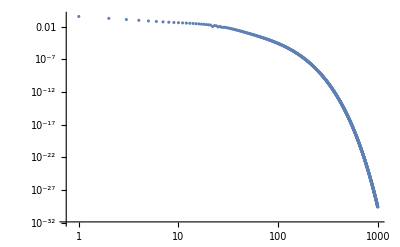

```mathematica
ListLogLogPlot[Array[relerrEamp[[#,#]]&,spinmax]]
```